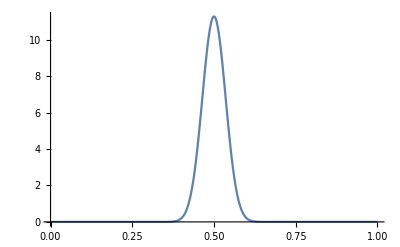

```mathematica
Plot[PDF[BetaDistribution[100,100],x],{x,0,1},PlotRange->All]
```

```mathematica
OneDimentionMoyalBracket[A_,H_,x_,p_,end_]:=Sum[(-1)^j/((2j+1)!)*(h/4Pi)^(2j)*
Sum[Binomial[2j+1,k]*(-1)^(2j+1-k)*
Nest[D[#,p]&,Nest[D[#,x]&,A,k],2j+1-k]*Nest[D[#,x]&,Nest[D[#,p]&,H,k],2j+1-k]
,{k,0,2j+1}],{j,0,end}];
```

```mathematica
Bracket[A_,H_,xList_,pList_,end_]:=Sum[(-1)^j/((2j+1)!)*(h/4Pi)^(2j)*
Sum[Binomial[2j+1,k]*(-1)^(2j+1-k)*
Nest[D[#,p]&,Nest[D[#,x]&,A,k],2j+1-k]*Nest[D[#,x]&,Nest[D[#,p]&,H,k],2j+1-k]
,{k,0,2j+1}],{j,0,end}]
```

```mathematica
MoyalBracket[f[x],p^2/(2m)+V[x],x,p,1]//Simplify
```

(p f'[x])/m

```mathematica
Binomial[2j+1,1]
```

1+2 j

```mathematica
MoyalBracket[p,p^2/(2m)+V[x],x,p,10]//Simplify
```

-V'[x]

```mathematica
MoyalBracket[-p/m*V'[x],p^2/(2m)+V[x],x,p,10]
```

V'[x]^2/m-(p^2 V''[x])/m^2

```mathematica
MoyalBracket[p^3,p^2/(2m)+V[x],x,p,10]
```

-3 p^2 V'[x]+1/16 h^2 π^2 V^(3)[x]

```mathematica
NestList[MoyalBracket[#,p^2/(2m)+V[x],x,p,10]&,x,7]
```

{x,p/m,-V'[x]/m,-(p V''[x])/m^2,(V'[x] V''[x])/m^2-(p^2 V^(3)[x])/m^3,(2 p V'[x] V^(3)[x])/m^3+(p (V''[x]^2/m^2+(V'[x] V^(3)[x])/m^2-(p^2 V^(4)[x])/m^3))/m,-(h^2 π^2 V^(3)[x] V^(4)[x])/(16 m^4)-V'[x] ((2 V'[x] V^(3)[x])/m^3-(2 p^2 V^(4)[x])/m^4+(V''[x]^2/m^2+(V'[x] V^(3)[x])/m^2-(p^2 V^(4)[x])/m^3)/m)+(p ((2 p V''[x] V^(3)[x])/m^3+(2 p V'[x] V^(4)[x])/m^3+(p ((3 V''[x] V^(3)[x])/m^2+(V'[x] V^(4)[x])/m^2-(p^2 V^(5)[x])/m^3))/m))/m,-(h^2 p π^2 V^(3)[x] V^(5)[x])/(4 m^5)-V'[x] ((6 p V'[x] V^(4)[x])/m^4+(p ((2 V''[x] V^(3)[x])/m^3+(2 V'[x] V^(4)[x])/m^3-(2 p^2 V^(5)[x])/m^4+((3 V''[x] V^(3)[x])/m^2+(V'[x] V^(4)[x])/m^2-(p^2 V^(5)[x])/m^3)/m))/m+((2 p V''[x] V^(3)[x])/m^3+(2 p V'[x] V^(4)[x])/m^3+(p ((3 V''[x] V^(3)[x])/m^2+(V'[x] V^(4)[x])/m^2-(p^2 V^(5)[x])/m^3))/m)/m)+1/m p (-(h^2 π^2 (V^(4)[x])^2)/(16 m^4)-V''[x] ((2 V'[x] V^(3)[x])/m^3-(2 p^2 V^(4)[x])/m^4+(V''[x]^2/m^2+(V'[x] V^(3)[x])/m^2-(p^2 V^(4)[x])/m^3)/m)-(h^2 π^2 V^(3)[x] V^(5)[x])/(16 m^4)-V'[x] ((2 V''[x] V^(3)[x])/m^3+(2 V'[x] V^(4)[x])/m^3-(2 p^2 V^(5)[x])/m^4+((3 V''[x] V^(3)[x])/m^2+(V'[x] V^(4)[x])/m^2-(p^2 V^(5)[x])/m^3)/m)+(p ((2 p (V^(3)[x])^2)/m^3+(4 p V''[x] V^(4)[x])/m^3+(2 p V'[x] V^(5)[x])/m^3+(p ((3 (V^(3)[x])^2)/m^2+(4 V''[x] V^(4)[x])/m^2+(V'[x] V^(5)[x])/m^2-(p^2 V^(6)[x])/m^3))/m))/m)}

```mathematica
NestList[MoyalBracket[#,p^2/(2m)-1/x,x,p,10]&,x,7]
```

{x,p/m,-1/(m x^2),(2 p)/(m^2 x^3),-2/(m^2 x^5)-(6 p^2)/(m^3 x^4),(p (10/(m^2 x^6)+(24 p^2)/(m^3 x^5)))/m+(12 p)/(m^3 x^6),(p ((p (-60/(m^2 x^7)-(120 p^2)/(m^3 x^6)))/m-(72 p)/(m^3 x^7)))/m+(9 h^2 π^2)/(m^4 x^9)-((10/(m^2 x^6)+(24 p^2)/(m^3 x^5))/m+12/(m^3 x^6)+(48 p^2)/(m^4 x^5))/x^2,(p ((p ((p (420/(m^2 x^8)+(720 p^2)/(m^3 x^7)))/m+(504 p)/(m^3 x^8)))/m-(81 h^2 π^2)/(m^4 x^10)+(2 ((10/(m^2 x^6)+(24 p^2)/(m^3 x^5))/m+12/(m^3 x^6)+(48 p^2)/(m^4 x^5)))/x^3-((-60/(m^2 x^7)-(120 p^2)/(m^3 x^6))/m-72/(m^3 x^7)-(240 p^2)/(m^4 x^6))/x^2))/m-(180 h^2 p π^2)/(m^5 x^10)-(((p (-60/(m^2 x^7)-(120 p^2)/(m^3 x^6)))/m-(72 p)/(m^3 x^7))/m+(p ((-60/(m^2 x^7)-(120 p^2)/(m^3 x^6))/m-72/(m^3 x^7)-(240 p^2)/(m^4 x^6)))/m-(144 p)/(m^4 x^7))/x^2}

```mathematica
f:=#^2&;
f^2
```

(#1^2&)^(2[5])

```mathematica
Table[{A[i,leftorright,times],P[i,leftorright,times]},{i,1,3}]
```

{{A[1,leftorright,times],P[1,leftorright,times]},{A[2,leftorright,times],P[2,leftorright,times]},{A[3,leftorright,times],P[3,leftorright,times]}}

```mathematica
Cases[FullForm[a^3,_Power,Infinity]
```

{a^3}

```mathematica
Cases[FullForm[a[1,2]^3],_Power,Infinity]
```

{a[1,2]^3}

```mathematica
Cases[FullForm[Expand[Total[A[#1]*B[#2]-A[#2]B[#1]&@@@{{x1,p1},{x2,p2},{x3,p3}}]^3]],_Power,Infinity]
```

{A[x1]^3,B[p1]^3,A[x1]^2,B[p1]^2,A[x2]^2,B[p2]^2,A[x2]^3,B[p2]^3,A[x1]^2,B[p1]^2,A[x2]^2,B[p2]^2,A[x3]^2,B[p3]^2,A[x3]^2,B[p3]^2,A[x3]^3,B[p3]^3,A[x1]^2,B[p1]^2,A[x2]^2,B[p2]^2,A[x3]^2,B[p3]^2,A[p1]^2,B[x1]^2,A[p1]^2,B[x1]^2,A[p1]^2,B[x1]^2,A[p1]^3,B[x1]^3,A[x1]^2,B[p1]^2,A[x2]^2,B[p2]^2,A[x3]^2,B[p3]^2,A[p1]^2,B[x1]^2,A[p2]^2,B[x2]^2,A[p2]^2,B[x2]^2,A[p2]^2,B[x2]^2,A[p2]^2,B[x2]^2,A[p2]^3,B[x2]^3,A[x1]^2,B[p1]^2,A[x2]^2,B[p2]^2,A[x3]^2,B[p3]^2,A[p1]^2,B[x1]^2,A[p2]^2,B[x2]^2,A[p3]^2,B[x3]^2,A[p3]^2,B[x3]^2,A[p3]^2,B[x3]^2,A[p3]^2,B[x3]^2,A[p3]^2,B[x3]^2,A[p3]^3,B[x3]^3}

```mathematica
Module[{A,B},
ReleaseHold[Hold[FullForm@Expand[Total[A[#1]*B[#2]-A[#2]B[#1]&@@@{{x1,p1},{x2,p2},{x3,p3}}]^3]]/.Plus->List]
]
```

List[Plus[Times[Power[A$22373[x1],3],Power[B$22373[p1],3]],Times[3,Power[A$22373[x1],2],A$22373[x2],Power[B$22373[p1],2],B$22373[p2]],Times[3,A$22373[x1],Power[A$22373[x2],2],B$22373[p1],Power[B$22373[p2],2]],Times[Power[A$22373[x2],3],Power[B$22373[p2],3]],Times[3,Power[A$22373[x1],2],A$22373[x3],Power[B$22373[p1],2],B$22373[p3]],Times[6,A$22373[x1],A$22373[x2],A$22373[x3],B$22373[p1],B$22373[p2],B$22373[p3]],Times[3,Power[A$22373[x2],2],A$22373[x3],Power[B$22373[p2],2],B$22373[p3]],Times[3,A$22373[x1],Power[A$22373[x3],2],B$22373[p1],Power[B$22373[p3],2]],Times[3,A$22373[x2],Power[A$22373[x3],2],B$22373[p2],Power[B$22373[p3],2]],Times[Power[A$22373[x3],3],Power[B$22373[p3],3]]],Plus[Times[-1,Power[A$22373[p1],3],Power[B$22373[x1],3]],Times[-3,Power[A$22373[p1],2],A$22373[p2],Power[B$22373[x1],2],B$22373[x2]],Times[-3,A$22373[p1],Power[A$22373[p2],2],B$22373[x1],Power[B$22373[x2],2]],Times[-1,Power[A$22373[p2],3],Power[B$22373[x2],3]],Times[-3,Power[A$22373[p1],2],A$22373[p3],Power[B$22373[x1],2],B$22373[x3]],Times[-6,A$22373[p1],A$22373[p2],A$22373[p3],B$22373[x1],B$22373[x2],B$22373[x3]],Times[-3,Power[A$22373[p2],2],A$22373[p3],Power[B$22373[x2],2],B$22373[x3]],Times[-3,A$22373[p1],Power[A$22373[p3],2],B$22373[x1],Power[B$22373[x3],2]],Times[-3,A$22373[p2],Power[A$22373[p3],2],B$22373[x2],Power[B$22373[x3],2]],Times[-1,Power[A$22373[p3],3],Power[B$22373[x3],3]]]]

```mathematica
ReleaseHold[Hold[2^3]/.Power->List]
```

{2,3}

```mathematica
FullForm[Expand[Total[A[#1]*B[#2]-A[#2]B[#1]&@@@{{x1,p1},{x2,p2},{x3,p3}}]^3]]
```

Plus[Times[Power[A[x1],3],Power[B[p1],3]],Times[3,Power[A[x1],2],A[x2],Power[B[p1],2],B[p2]],Times[3,A[x1],Power[A[x2],2],B[p1],Power[B[p2],2]],Times[Power[A[x2],3],Power[B[p2],3]],Times[3,Power[A[x1],2],A[x3],Power[B[p1],2],B[p3]],Times[6,A[x1],A[x2],A[x3],B[p1],B[p2],B[p3]],Times[3,Power[A[x2],2],A[x3],Power[B[p2],2],B[p3]],Times[3,A[x1],Power[A[x3],2],B[p1],Power[B[p3],2]],Times[3,A[x2],Power[A[x3],2],B[p2],Power[B[p3],2]],Times[Power[A[x3],3],Power[B[p3],3]],Times[-3,A[p1],Power[A[x1],2],Power[B[p1],2],B[x1]],Times[-6,A[p1],A[x1],A[x2],B[p1],B[p2],B[x1]],Times[-3,A[p1],Power[A[x2],2],Power[B[p2],2],B[x1]],Times[-6,A[p1],A[x1],A[x3],B[p1],B[p3],B[x1]],Times[-6,A[p1],A[x2],A[x3],B[p2],B[p3],B[x1]],Times[-3,A[p1],Power[A[x3],2],Power[B[p3],2],B[x1]],Times[3,Power[A[p1],2],A[x1],B[p1],Power[B[x1],2]],Times[3,Power[A[p1],2],A[x2],B[p2],Power[B[x1],2]],Times[3,Power[A[p1],2],A[x3],B[p3],Power[B[x1],2]],Times[-1,Power[A[p1],3],Power[B[x1],3]],Times[-3,A[p2],Power[A[x1],2],Power[B[p1],2],B[x2]],Times[-6,A[p2],A[x1],A[x2],B[p1],B[p2],B[x2]],Times[-3,A[p2],Power[A[x2],2],Power[B[p2],2],B[x2]],Times[-6,A[p2],A[x1],A[x3],B[p1],B[p3],B[x2]],Times[-6,A[p2],A[x2],A[x3],B[p2],B[p3],B[x2]],Times[-3,A[p2],Power[A[x3],2],Power[B[p3],2],B[x2]],Times[6,A[p1],A[p2],A[x1],B[p1],B[x1],B[x2]],Times[6,A[p1],A[p2],A[x2],B[p2],B[x1],B[x2]],Times[6,A[p1],A[p2],A[x3],B[p3],B[x1],B[x2]],Times[-3,Power[A[p1],2],A[p2],Power[B[x1],2],B[x2]],Times[3,Power[A[p2],2],A[x1],B[p1],Power[B[x2],2]],Times[3,Power[A[p2],2],A[x2],B[p2],Power[B[x2],2]],Times[3,Power[A[p2],2],A[x3],B[p3],Power[B[x2],2]],Times[-3,A[p1],Power[A[p2],2],B[x1],Power[B[x2],2]],Times[-1,Power[A[p2],3],Power[B[x2],3]],Times[-3,A[p3],Power[A[x1],2],Power[B[p1],2],B[x3]],Times[-6,A[p3],A[x1],A[x2],B[p1],B[p2],B[x3]],Times[-3,A[p3],Power[A[x2],2],Power[B[p2],2],B[x3]],Times[-6,A[p3],A[x1],A[x3],B[p1],B[p3],B[x3]],Times[-6,A[p3],A[x2],A[x3],B[p2],B[p3],B[x3]],Times[-3,A[p3],Power[A[x3],2],Power[B[p3],2],B[x3]],Times[6,A[p1],A[p3],A[x1],B[p1],B[x1],B[x3]],Times[6,A[p1],A[p3],A[x2],B[p2],B[x1],B[x3]],Times[6,A[p1],A[p3],A[x3],B[p3],B[x1],B[x3]],Times[-3,Power[A[p1],2],A[p3],Power[B[x1],2],B[x3]],Times[6,A[p2],A[p3],A[x1],B[p1],B[x2],B[x3]],Times[6,A[p2],A[p3],A[x2],B[p2],B[x2],B[x3]],Times[6,A[p2],A[p3],A[x3],B[p3],B[x2],B[x3]],Times[-6,A[p1],A[p2],A[p3],B[x1],B[x2],B[x3]],Times[-3,Power[A[p2],2],A[p3],Power[B[x2],2],B[x3]],Times[3,Power[A[p3],2],A[x1],B[p1],Power[B[x3],2]],Times[3,Power[A[p3],2],A[x2],B[p2],Power[B[x3],2]],Times[3,Power[A[p3],2],A[x3],B[p3],Power[B[x3],2]],Times[-3,A[p1],Power[A[p3],2],B[x1],Power[B[x3],2]],Times[-3,A[p2],Power[A[p3],2],B[x2],Power[B[x3],2]],Times[-1,Power[A[p3],3],Power[B[x3],3]]]

```mathematica
Module[{A,B},
Map[If[MatchQ[#,_List]&&Cases[FullForm[#],_A],Nest@@#]&,ReleaseHold[Hold[Evaluate@Expand[Total[A[#1]*B[#2]-A[#2]B[#1]&@@@{{x1,p1},{x2,p2},{x3,p3}}]^3]]/.{Plus->List,Power->List,Times->List}],{2}]]
```

Nest::argrx: Nest called with 2 arguments; 3 arguments are expected.

General::stop: Further output of Nest::argrx will be suppressed during this calculation.

{{Nest[∂_x1 #1&,3],Nest[∂_p1 #2&,3]},{Null,Nest[∂_x1 #1&,2],Null,Nest[∂_p1 #2&,2],Null},{Null,Null,Nest[∂_x2 #1&,2],Null,Nest[∂_p2 #2&,2]},{Nest[∂_x2 #1&,3],Nest[∂_p2 #2&,3]},{Null,Nest[∂_x1 #1&,2],Null,Nest[∂_p1 #2&,2],Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Nest[∂_x2 #1&,2],Null,Nest[∂_p2 #2&,2],Null},{Null,Null,Nest[∂_x3 #1&,2],Null,Nest[∂_p3 #2&,2]},{Null,Null,Nest[∂_x3 #1&,2],Null,Nest[∂_p3 #2&,2]},{Nest[∂_x3 #1&,3],Nest[∂_p3 #2&,3]},{Null,Null,Nest[∂_x1 #1&,2],Nest[∂_p1 #2&,2],Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Nest[∂_x2 #1&,2],Nest[∂_p2 #2&,2],Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Nest[∂_x3 #1&,2],Nest[∂_p3 #2&,2],Null},{Null,Nest[∂_p1 #1&,2],Null,Null,Nest[∂_x1 #2&,2]},{Null,Nest[∂_p1 #1&,2],Null,Null,Nest[∂_x1 #2&,2]},{Null,Nest[∂_p1 #1&,2],Null,Null,Nest[∂_x1 #2&,2]},{Null,Nest[∂_p1 #1&,3],Nest[∂_x1 #2&,3]},{Null,Null,Nest[∂_x1 #1&,2],Nest[∂_p1 #2&,2],Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Nest[∂_x2 #1&,2],Nest[∂_p2 #2&,2],Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Nest[∂_x3 #1&,2],Nest[∂_p3 #2&,2],Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Nest[∂_p1 #1&,2],Null,Nest[∂_x1 #2&,2],Null},{Null,Nest[∂_p2 #1&,2],Null,Null,Nest[∂_x2 #2&,2]},{Null,Nest[∂_p2 #1&,2],Null,Null,Nest[∂_x2 #2&,2]},{Null,Nest[∂_p2 #1&,2],Null,Null,Nest[∂_x2 #2&,2]},{Null,Null,Nest[∂_p2 #1&,2],Null,Nest[∂_x2 #2&,2]},{Null,Nest[∂_p2 #1&,3],Nest[∂_x2 #2&,3]},{Null,Null,Nest[∂_x1 #1&,2],Nest[∂_p1 #2&,2],Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Nest[∂_x2 #1&,2],Nest[∂_p2 #2&,2],Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Nest[∂_x3 #1&,2],Nest[∂_p3 #2&,2],Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Nest[∂_p1 #1&,2],Null,Nest[∂_x1 #2&,2],Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null},{Null,Nest[∂_p2 #1&,2],Null,Nest[∂_x2 #2&,2],Null},{Null,Nest[∂_p3 #1&,2],Null,Null,Nest[∂_x3 #2&,2]},{Null,Nest[∂_p3 #1&,2],Null,Null,Nest[∂_x3 #2&,2]},{Null,Nest[∂_p3 #1&,2],Null,Null,Nest[∂_x3 #2&,2]},{Null,Null,Nest[∂_p3 #1&,2],Null,Nest[∂_x3 #2&,2]},{Null,Null,Nest[∂_p3 #1&,2],Null,Nest[∂_x3 #2&,2]},{Null,Nest[∂_p3 #1&,3],Nest[∂_x3 #2&,3]}}

```mathematica
Hold[Evaluate@Expand[Total[A[#1]*B[#2]-A[#2]B[#1]&@@@{{x1,p1},{x2,p2},{x3,p3}}]^3]]
```

Hold[A[x1]^3 B[p1]^3+3 A[x1]^2 A[x2] B[p1]^2 B[p2]+3 A[x1] A[x2]^2 B[p1] B[p2]^2+A[x2]^3 B[p2]^3+3 A[x1]^2 A[x3] B[p1]^2 B[p3]+6 A[x1] A[x2] A[x3] B[p1] B[p2] B[p3]+3 A[x2]^2 A[x3] B[p2]^2 B[p3]+3 A[x1] A[x3]^2 B[p1] B[p3]^2+3 A[x2] A[x3]^2 B[p2] B[p3]^2+A[x3]^3 B[p3]^3-3 A[p1] A[x1]^2 B[p1]^2 B[x1]-6 A[p1] A[x1] A[x2] B[p1] B[p2] B[x1]-3 A[p1] A[x2]^2 B[p2]^2 B[x1]-6 A[p1] A[x1] A[x3] B[p1] B[p3] B[x1]-6 A[p1] A[x2] A[x3] B[p2] B[p3] B[x1]-3 A[p1] A[x3]^2 B[p3]^2 B[x1]+3 A[p1]^2 A[x1] B[p1] B[x1]^2+3 A[p1]^2 A[x2] B[p2] B[x1]^2+3 A[p1]^2 A[x3] B[p3] B[x1]^2-A[p1]^3 B[x1]^3-3 A[p2] A[x1]^2 B[p1]^2 B[x2]-6 A[p2] A[x1] A[x2] B[p1] B[p2] B[x2]-3 A[p2] A[x2]^2 B[p2]^2 B[x2]-6 A[p2] A[x1] A[x3] B[p1] B[p3] B[x2]-6 A[p2] A[x2] A[x3] B[p2] B[p3] B[x2]-3 A[p2] A[x3]^2 B[p3]^2 B[x2]+6 A[p1] A[p2] A[x1] B[p1] B[x1] B[x2]+6 A[p1] A[p2] A[x2] B[p2] B[x1] B[x2]+6 A[p1] A[p2] A[x3] B[p3] B[x1] B[x2]-3 A[p1]^2 A[p2] B[x1]^2 B[x2]+3 A[p2]^2 A[x1] B[p1] B[x2]^2+3 A[p2]^2 A[x2] B[p2] B[x2]^2+3 A[p2]^2 A[x3] B[p3] B[x2]^2-3 A[p1] A[p2]^2 B[x1] B[x2]^2-A[p2]^3 B[x2]^3-3 A[p3] A[x1]^2 B[p1]^2 B[x3]-6 A[p3] A[x1] A[x2] B[p1] B[p2] B[x3]-3 A[p3] A[x2]^2 B[p2]^2 B[x3]-6 A[p3] A[x1] A[x3] B[p1] B[p3] B[x3]-6 A[p3] A[x2] A[x3] B[p2] B[p3] B[x3]-3 A[p3] A[x3]^2 B[p3]^2 B[x3]+6 A[p1] A[p3] A[x1] B[p1] B[x1] B[x3]+6 A[p1] A[p3] A[x2] B[p2] B[x1] B[x3]+6 A[p1] A[p3] A[x3] B[p3] B[x1] B[x3]-3 A[p1]^2 A[p3] B[x1]^2 B[x3]+6 A[p2] A[p3] A[x1] B[p1] B[x2] B[x3]+6 A[p2] A[p3] A[x2] B[p2] B[x2] B[x3]+6 A[p2] A[p3] A[x3] B[p3] B[x2] B[x3]-6 A[p1] A[p2] A[p3] B[x1] B[x2] B[x3]-3 A[p2]^2 A[p3] B[x2]^2 B[x3]+3 A[p3]^2 A[x1] B[p1] B[x3]^2+3 A[p3]^2 A[x2] B[p2] B[x3]^2+3 A[p3]^2 A[x3] B[p3] B[x3]^2-3 A[p1] A[p3]^2 B[x1] B[x3]^2-3 A[p2] A[p3]^2 B[x2] B[x3]^2-A[p3]^3 B[x3]^3]

```mathematica
FullForm[A[o1]]
```

A[o1]

```mathematica
Cases[A[o1],_A]
```

{}

```mathematica
ReleaseHold[Hold[Evaluate@Expand[Total[{A,a}*{B,b}-{B,a}*{B,a}&@@@{{x1,p1},{x2,p2},{x3,p3}}]^3]]/.{Plus->List,Power->List,Times->List}]
```

{{{27,{A,3},{B,3}},{-81,{A,2},{B,4}},{81,A,{B,5}},{-27,{B,6}}},{{-27,{a,6}},{81,{a,5},b},{-81,{a,4},{b,2}},{27,{a,3},{b,3}}}}